```mathematica
allGraphs=Association[];
```

```mathematica
veryEmptyMat={{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}
```

{{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}}

```mathematica
(*Monitor[ComputeGraph[veryEmptyMat,16],{globalDepth,Length[allGraphs]}]*)
```

```mathematica
ForceZero[key_]:=Block[{result=0},
If[ToString[allGraphs[key,"comp"]]≠"Equal",
If[ToString[allGraphs[key,"comp"]]=="Greater",
Print["Problem with key ", key];
Interrupt[];
];
allGraphs[key,"comp"]=Equal;
allGraphs[key,"compwhy"]="forced to zero (recursive)";
result+=1;
];
Table[
result+=ForceZero[child]
,{child,Flatten[allGraphs[key,"children"]]}
];
result
];
```

```mathematica
Monitor[ComputeGraph[veryEmptyMat,16],{globalDepth,Length[allGraphs]}]
```

0

```mathematica
Length[allGraphs]
```

127

```mathematica
alfaKey=35977;
betaKey=31681;
gammaKey=23041 ;
deltaKey=20803;
epsilonKey=27259;
alfa1Key=36166;
beta1Key=31738;
gamma1Key=29608;
delta1Key=36112;
epsilon1Key=31714;
lambdaKey=20665;
k5Key=29524;
```

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,123},{GreaterEqual,4}}

```mathematica
(*Table[ForceZero[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]*)
```

## Now compute the inequalities

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
ineqsSimplified=AndToTable[Simplify[Fold[And,ineqsPure]]];
```

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsSimplified,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]]
```

{}

```mathematica
fullVariables=Map[First,repZero]
```

{}

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k],If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
repcolofour5graph=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold,If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
ineqsSimplified
```

{v1234>0,v123x4>0,v124x3>0,v12x34>0,v12x3x4>0,v134x2>0,v13x24≥0,v13x2x4≥0,v14x23>0,v14x2x3>0,v1x234>0,v1x23x4>0,v1x24x3≥0,v1x2x34>0,v1x2x3x4≥0,v1x24x3+v1x2x3x4>0,v13x24+v13x2x4>0,v13x2x4+v1x2x3x4>0,v13x24+v1x24x3>0}

## Now we are going to use the information in the inequalities to set some graph to positive

```mathematica
PositiveExpressions = Map[First,Select[ineqsSimplified,ToString[#[[0]]]=="Greater"&]]
```

{v1234,v123x4,v124x3,v12x34,v12x3x4,v134x2,v14x23,v14x2x3,v1x234,v1x23x4,v1x2x34,v1x24x3+v1x2x3x4,v13x24+v13x2x4,v13x2x4+v1x2x3x4,v13x24+v1x24x3}

```mathematica
Table[
Table[
If[ToString[allGraphs[key,"comp"]]≠"Greater",
Print[key, " was " ,allGraphs[key,"comp"]];
allGraphs[key,"comp"]=Greater;
allGraphs[key,"compwhy"]="Expression " <> ToString[pos] <> " is positive from step 1 ";
]
 ,
{key,Select[Keys[allGraphs],allGraphs[#,"colofour"]==pos&]}
],{pos, PositiveExpressions}]
```

{{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null},{Null}}

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
base5Keys = Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&];Length[base5Keys]
```

15

```mathematica
Table[allGraphs[k,"comp"],{k,base5Keys}]//Tally
```

{{GreaterEqual,4},{Greater,11}}

```mathematica
goodAtoms=Select[base5Keys,ToString[allGraphs[#,"comp"]]=="Greater"&];Length[goodAtoms]
```

11

```mathematica
Table[allGraphs[k,"colofour"],{k,goodAtoms}]/.repcolofour5graph
```

{-Graphics-v1x2x34365,-Graphics-v1x23x4373,-Graphics-v1x234377,-Graphics-v14x2x3391,-Graphics-v14x23400,-Graphics-v134x2473,-Graphics-v12x3x4607,-Graphics-v12x34608,-Graphics-v124x3637,-Graphics-v123x4697,-Graphics-v1234728}

```mathematica
problematicAtoms=Select[base5Keys,ToString[allGraphs[#,"comp"]]=="GreaterEqual"&];Length[problematicAtoms]
```

4

```mathematica
Table[allGraphs[k,"colofour"],{k,problematicAtoms}]/.repcolofour5graph
```

{-Graphics-v1x2x3x4364,-Graphics-v1x24x3367,-Graphics-v13x2x4445,-Graphics-v13x24448}

```mathematica
allGraphs[alfa1Key,"colofour"]/.repcolofour5graph
```

Missing[KeyAbsent,36166]

```mathematica
ExpressionToTable[Select[ineqsSimplified,#[[0]]==Greater&]]/.repcolofour5graph
```

-Graphics-v1x234377>0
-Graphics-v1234728>0
-Graphics-v14x2x3391>0
-Graphics-v1x23x4373>0
-Graphics-v12x3x4607>0
-Graphics-v123x4697>0
-Graphics-v134x2473>0
-Graphics-v124x3637>0
-Graphics-v14x23400>0
-Graphics-v1x2x34365>0
-Graphics-v12x34608>0
-Graphics-v13x2x4445+-Graphics-v1x2x3x4364>0
-Graphics-v13x24448+-Graphics-v13x2x4445>0
-Graphics-v1x24x3367+-Graphics-v1x2x3x4364>0
-Graphics-v13x24448+-Graphics-v1x24x3367>0

## Now compute the inequalities (part II)

```mathematica
ineqsPure=Monitor[Table[allGraphs[k]["comp"][allGraphs[k]["colofour"],0],{k,Keys[allGraphs]}],k]//DeleteDuplicates;
```

```mathematica
ineqsSimplified=AndToTable[Simplify[Fold[And,ineqsPure]]];
```

```mathematica
repZero=Map[#[[1]]->#[[2]]&,Select[ineqsSimplified,ToString[#[[0]]]=="Equal"&&Length[DeleteDuplicates[ListofVars[#]]]==1&]]
```

{}

```mathematica
fullVariables=Map[First,repZero]
```

{}

```mathematica
repcolofour5textBase=Table[allGraphs[k,"colofour"]->Style[allGraphs[k,"colofour"],ColourForKey[allGraphs,k],If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
repcolofour5graph=Table[allGraphs[k,"colofour"]->Framed[Labeled[allGraphs[k,"graph"],{Style[allGraphs[k,"colofour"],Bold,If[MemberQ[fullVariables,allGraphs[k,"colofour"]],Underlined,Plain]],Style[k,ColourForKey[allGraphs,k]]},{Top,Bottom}]],{k,Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]}];
```

```mathematica
ineqsSimplified
```

{v1234>0,v123x4>0,v124x3>0,v12x34>0,v12x3x4>0,v134x2>0,v13x24≥0,v13x2x4≥0,v14x23>0,v14x2x3>0,v1x234>0,v1x23x4>0,v1x24x3≥0,v1x2x34>0,v1x2x3x4≥0,v1x24x3+v1x2x3x4>0,v13x24+v13x2x4>0,v13x2x4+v1x2x3x4>0,v13x24+v1x24x3>0}

```mathematica
ExpressionToTable[Select[ineqsSimplified,Length[ListofVars[#]]>1&&#[[0]]==Greater&]]/.repcolofour5graph
```

-Graphics-v13x2x4445+-Graphics-v1x2x3x4364>0
-Graphics-v13x24448+-Graphics-v13x2x4445>0
-Graphics-v1x24x3367+-Graphics-v1x2x3x4364>0
-Graphics-v13x24448+-Graphics-v1x24x3367>0

```mathematica
pr=Problems[allGraphs,0]//Sort
```

{283→364,283→445,286→367,286→448,361→364,361→367,442→445,442→448}

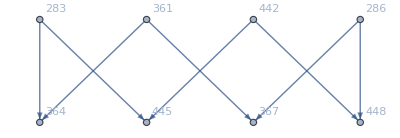

```mathematica
gr2=Graph[pr,VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
```

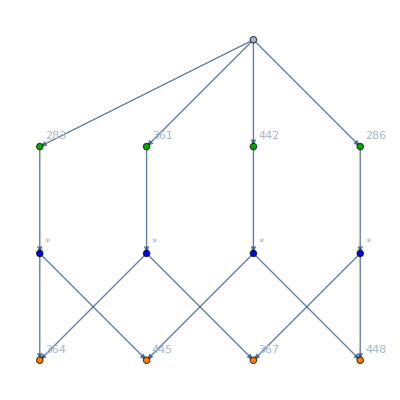

```mathematica
Graph[DependencyGraph[allGraphs,{283,361,442,286}],GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
Graph[DependencyGraph6[allGraphs,{283,361,442,286}],GraphLayout->"HighDimensionalEmbedding"]
```

Graph[DependencyGraph6[<|0→<|signature→0,12,colortable→{{v1234+v123x4+v124x3+v12x34+v12x3x4,v134x2+v13x24+v13x2x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v123x4+v134x2+v13x24+v13x2x4,v124x3+v12x34+v12x3x4+v14x23+v14x2x3+v1x234+v1x23x4+v1x24x3+v1x2x34+v1x2x3x4},{v1234+v124x3+v134x2+v14x23+v14x2x3,1},{1},{v1234+v124x3+v13x24+v1x234+v1x24x3,v123x4+v12x34+v12x3x4+v134x2+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x2x34+v1x2x3x4},{v1234+v12x34+v134x2+v1x234+v1x2x34,v123x4+v124x3+v12x3x4+v13x24+v13x2x4+v14x23+v14x2x3+v1x23x4+v1x24x3+v1x2x3x4}}|>,125,2→<|1|>|>,{283,3}],1]
 |  |  |  |

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,123},{GreaterEqual,4}}

```mathematica
ExpressionsToGraph6[list_]:=Block[{result={},left,newNode=-1,currentBis,vertexLabels, vertices={},key,mat2,vertexStyle={},vertexLabels2={},vertexStyle2={},sumKey,crit},
Table[
If[Length[current]==0,
result=Append[result,current->newNode ],

currentBis=current;
crit = Fold[Plus,current];
sumKey=First[Select[Keys[allGraphs],(allGraphs[#,"colofour"]==crit)/.repZero&]];
newNode=sumKey;
vertexLabels2=Append[vertexLabels2,sumKey->Tooltip[allGraphs[sumKey,"graph"],sumKey]];
vertexStyle2=Append[vertexStyle2,sumKey->ColourForKey[allGraphs,sumKey]];
Table[
result=Append[result,currentBis[[k]]->newNode];
vertices=Append[vertices,currentBis[[k]]]
,{k,Length[currentBis]}
];
];

(*result=Append[result,newNode->0];*)
newNode=newNode-1
,
{current,list}
];
vertices = DeleteDuplicates[vertices];
vertexLabels=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;
mat2=allGraphs[key,"matrix"];
v->Tooltip[
Labeled[
allGraphs[key]["graph"],allGraphs[key]["colofour"]],
Labeled[
Column[
{
Style[key,Bold],
MatrixForm[mat2,TableHeadings->{Table[Style[k,Red],{k,TheSize}],Table[Style[k,Red],{k,TheSize}]}]
,
Row[{
allGraphs[key]["graph"],
Graph[
VertexList[allGraphs[key]["graph"]],
EdgeList[allGraphs[key]["graph"]],
VertexLabels->PropertyValue[allGraphs[key]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[allGraphs[key]["parents"],Italic],
Style[allGraphs[key]["colofour"],Italic]
},
Center
],Style[allGraphs[key]["compwhy"],Bold]]]

,{v,vertices}];
vertexStyle=Table[key=Select[Keys[allGraphs],allGraphs[#,"colofour"]==v&]//First;v->ColourForKey[allGraphs,key],{v,vertices}];
Graph[result,VertexLabels->Join[vertexLabels,vertexLabels2],VertexStyle->Join[vertexStyle,vertexStyle2]]
]
```

```mathematica
Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==4&&EdgeCount[g]==4]&]
```

{360,354,352,336,334,328,282,280,274,256,120,118,112,94,40}

```mathematica
allGraphs[280,"colofour"]
```

v13x24+v13x2x4+v1x24x3+v1x2x3x4

```mathematica
2*allGraphs[280,"colofour"]-(allGraphs[283,"colofour"]+allGraphs[361,"colofour"])//Simplify
```

2 v13x24+v13x2x4+v1x24x3

```mathematica
allGraphs["full"]=Association[]
```

<||>

```mathematica
allGraphs["full","graph"]=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,2<->5,3<->5,4<->5},VertexLabels->{1->1,2->2,3->3,4->4},ImageSize->{50,50}, EdgeStyle->Darker[Green], VertexStyle->Red,VertexSize->Small]
```

-Graphics-

## the following is not correct since we miss a factor 2:

```mathematica
allGraphs["full","colofour"]=v13x24+v13x2x4+v1x24x3
```

v13x24+v13x2x4+v1x24x3

```mathematica
allGraphs["full","comp"]=GreaterEqual
```

GreaterEqual

```mathematica
allGraphs["full","compwhy"]="To be proven"
```

To be proven

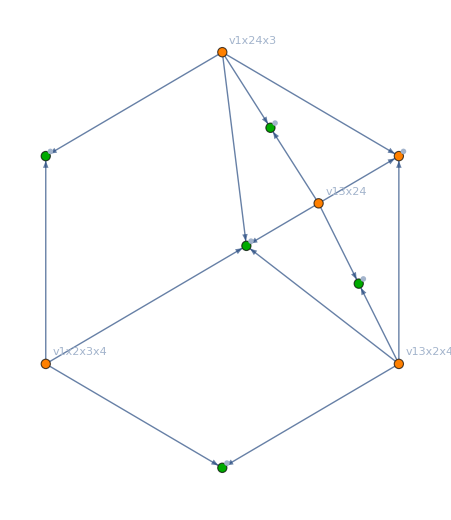

```mathematica
Graph[ExpressionsToGraph6[Join[Map[First,Select[ineqsSimplified,Length[ListofVars[#]]>1&&#[[0]]==Greater&]],{allGraphs[280,"colofour"],v13x24+v13x2x4+v1x24x3}]],GraphLayout->"TutteEmbedding"]
```

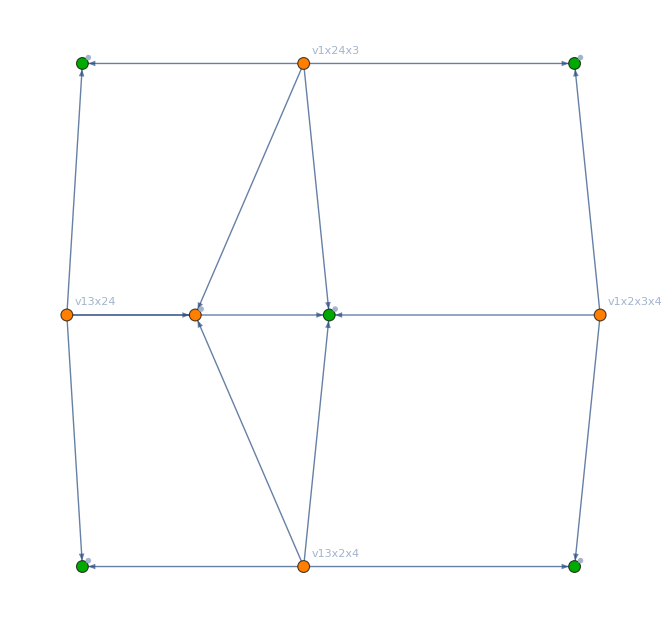

```mathematica
Graph[ExpressionsToGraph6[Join[Map[First,Select[ineqsSimplified,Length[ListofVars[#]]>1&&#[[0]]==Greater&]],{allGraphs[280,"colofour"],v13x24+v13x2x4+v1x24x3}]],GraphLayout->"HighDimensionalEmbedding"]
```